Created by: ruebenko on 12-07-2020 13:31:33

### Categorization

Tutorial

OpenCascadeLink

OpenCascadeLink`

OpenCascadeLink/tutorial/HelicalBevelGear

Synonyms

CAD

### Keywords

revolution

Loft

gear

bevel

bevel gear

helical gear

helical bevel gear

Details

# Helical Bevel Gear

The purpose of this tutorial is to illustrate the usage of the OpenCascadeLink to greate a helical bevel gear. The shape and the procedure of the creation are based on a computer aided design (CAD) tutorial [1].

-Graphics-

The creation of the gear will be done in several stages. First, the shaft is created. As a second step the gear will be made. Both the shaft and the gear will be combined. Following that the bosses are added and lastly the gear will be perforated.

Load the packages.

```mathematica
Needs["OpenCascadeLink`"]
Needs["NDSolve`FEM`"]
```

### Shaft

The shaft will be created by specifying a cross section in the X-Z plane. This cross section will then serve as  a basis for a solid created from a revolution around the X-axis.

-Graphics-

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shaft,"ShapeSurfaceMeshOptions"->{"LinearDeflection"->0.001}];
Show[
bmesh["Wireframe"["MeshElementStyle"->Directive[Opacity[0.3],FaceForm[LightGray],EdgeForm[]]]],
bmesh["Edgeframe"],
(*Graphics3D[{Polygon[{{0,0,0},{163,0,0},{163,0,50},{0,0,50}}]}],*)
OpenCascadeAxis3D[{-10,0,0},{200,75,75}]]
```

The cross section will consist of three parts, two line segments and a half circle.

Specify a cross section of the shaft:

```mathematica
length=163;
radius=11;
s1=Line[{{0,0,0},{0,0,45},{5,0,45},{5,0,39},{-112+length,0,39},{-112+length,0,38},{-80+length-2 radius,0,38},{-80+length-2 radius,0,36}}];
s2=OpenCascadeCircle[{{length-80-radius,0,36},{0,-1,0}},radius,{π,2π}];
s3=Line[{{-80+length,0,36},{-32+length,0,36},{-32+length,0,32.5},{length,0,32.5},{length,0,0},{0,0,0}}];
```

Note that the orientation of the segments is important. Should the orientation of the segments in the opposite direction the revolution will result in a solid that specifies the region outside of the shaft. If the orientation of a set of segments be in the opposite direction to what is wanted a trick is to revert the axis of revolution in the exact opposite direction. That will avoid respecifying the segments too.

Specify the cross section:

```mathematica
crossSection={s1,s2,s3};
```

Visualize the cross section of the shaft:

```mathematica
Show[
Graphics3D[crossSection/.OpenCascadeCircle->Circle3D],OpenCascadeAxis3D[{0,0,0},{200,25,50}],Boxed->False]
```

-Graphics3D-

Create OpenCascade objects from the cross section:

```mathematica
s=OpenCascadeShape/@crossSection
```

{OpenCascadeShapeExpression[1],OpenCascadeShapeExpression[2],OpenCascadeShapeExpression[3]}

Combine the segments into a single wire object

```mathematica
shape=OpenCascadeShapeWire[s]
OpenCascadeShapeType[shape]
```

OpenCascadeShapeExpression[4]

Wire

While OpenCascadeShapeUnion could have been used to combine the segments into a single object, OpenCascadeShapeUnion will return a compound and it’s harder to see what is in a compound.

Next, the cross section will be revolved around a rotation axis along the X-axis.

Create a rotation axis:

```mathematica
rotationAxis={{0,0,0},{200,0,0}};
Graphics3D[{crossSection/.OpenCascadeCircle->Circle3D,{Red,Arrow[rotationAxis]}}]
```

-Graphics3D-

Create the rotational sweep of the cross section around the rotation axis:

```mathematica
shaft=OpenCascadeShapeRotationalSweep[shape,rotationAxis]
```

OpenCascadeShapeExpression[5]

Inspect the type of the shape object created:

```mathematica
OpenCascadeShapeType[shaft]
```

Shell

Now that the cross section is rotated the resulting shape is a shell. That is because the input to the rotation was a wire. However, we would like to have a solid.

Create a solid from the shell and inspect the type:

```mathematica
shaft=OpenCascadeShapeSolid[shaft]
OpenCascadeShapeType[shaft]
```

OpenCascadeShapeExpression[6]

Solid

As an alternative, one could have used Polygon for the creation of the cross section. These are face type OpenCascade objects and after a revolution would have returned an OpenCascade solid.

Extract a boundary element mesh:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shaft(*,"ShapeSurfaceMeshOptions"->{"LinearDeflection"->0.001}*)]
```

ElementMesh[{{0.,163.},{-44.6719,44.6719},{-45.,45.}},Automatic]

Visualize the boundary element mesh of the shaft:

```mathematica
Show[
shaftGR=bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightGray]]]],
OpenCascadeAxis3D[{-10,0,0},{200,75,75}]]
```

-Graphics3D-

To verify that the boundary mesh construction worked as intended, a full element mesh is generated.

Create a full element mesh:

```mathematica
ToElementMesh[bmesh,"MeshOrder"->1]
```

ToElementMesh::femimq: The element mesh has insufficient quality of -3.51077×10^-16. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

ElementMesh[{{0.,163.},{-44.6719,44.6719},{-45.,45.}},{TetrahedronElement[<10052>]}]

The warning message will disappear if the boundary element mesh is created with a smaller "LinearDeflection" value than the default.

### Gears

The creation of the gear itself will be done in two steps. First half a gear tooth is modeled in the YZ-plane. The half tooth is constructed by combining three sections of circles. This half tooth is then mirrored at an axis to give a complete tooth. The the single tooth is rotated to make a set of gear teeth in the YZ-plane. Once that is done the gear in the YZ-pane is translated, rotated and scaled in a second plane parallel to the YZ-plane. This procedure is repeated one more time to give a third set of teeth in a third plane again parallel to YZ-plane. The actual gear is then created by extruding through the planes. This created a loft.

-Graphics-

```mathematica
temp1=OpenCascadeShapeLinearSweep[ocGearProfile1,{{0,0,0},{2,0,0}}];
temp2=OpenCascadeShapeLinearSweep[ocGearProfile2,{{0,0,0},{2,0,0}}];
temp3=OpenCascadeShapeLinearSweep[ocGearProfile3,{{0,0,0},{2,0,0}}];
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[ocGear];
Show[bmesh["Edgeframe"["EdgeframeDirective"->LightGray]],OpenCascadeShapeSurfaceMeshToBoundaryMesh[temp1]["Wireframe"["MeshElementStyle"->FaceForm[Red]]],
OpenCascadeShapeSurfaceMeshToBoundaryMesh[temp2]["Wireframe"["MeshElementStyle"->FaceForm[Red]]],
OpenCascadeShapeSurfaceMeshToBoundaryMesh[temp3]["Wireframe"["MeshElementStyle"->FaceForm[Red]]]]
```

#### Gear teeth

The gear tooth will be created by intersecting three circles and taking parts of their boundaries.

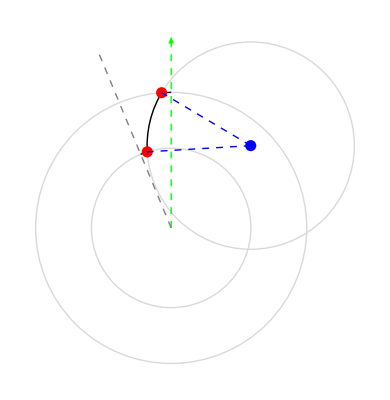

```mathematica
(* This works once the section has been evaluated *)
Graphics[{
{LightGray,Circle[{0,0},r1],Circle[{0,0},r2],Circle[cc,r3]},
Circle[{0,0},r1,{π/2,π-ArcCos[6/r1]}],
Circle[{0,0},r2,{π-ArcCos[15/r2],(π/2+2 π/16)}],
Circle[p3,r3,{θ1,2π+θ2}],
{Red,PointSize[0.02],Point[p1],Point[p2]},

{Blue,PointSize[0.02],Point[p3]},
{Blue,Dashed,Line[{p3,p1}],Line[{p3,p2}]},
{Green,Dashed,Arrow[{{0,0},{0,120}}]},
{Gray,Dashed,Line[{{0,0},120{Cos[θ],Sin[θ]}/.θ->(π/2+2 π/16)}]}}]
```

We start by sketching the procedure of the gear tooth generation in 2D.

Define different radii:

```mathematica
r1=85;
r2=50;
r3=65;
```

Specify the intersection points:

```mathematica
N[p1=r1 {Cos[θ],Sin[θ]}/.θ->(π-ArcCos[6/r1])]
N[p2=r2{Cos[θ],Sin[θ]}/.θ->(π-ArcCos[15/r2])]
```

{-6.,84.788}

{-15.,47.697}

Find the coordinate of the third circle such that is passes through the specified intersection points and has the given radius r3:

```mathematica
eqn=(x-x1)^2+(y-y1)^2==r3^2;
N[p3={x,y}/.Solve[{eqn/.Thread[Rule[{x1,y1},p1]],eqn/.Thread[Rule[{x1,y1},p2]],x>0,y>0},{x,y}][[1]]]
```

{49.8833,51.5907}

Visualize the three circles and the relevant intersections.

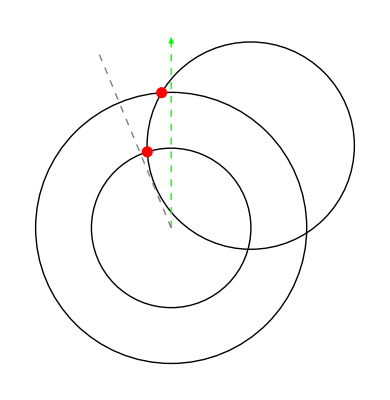

```mathematica
Graphics[{Circle[{0,0},r1],Circle[{0,0},r2],Circle[p3,r3],{Green,Dashed,Arrow[{{0,0},{0,120}}]},{Red,PointSize[0.02],Point[p1],Point[p2]},
{Gray,Dashed,Line[{{0,0},120{Cos[θ],Sin[θ]}/.θ->(π/2+2 π/16)}]}}]
```

Compute the arc angles for the circles from p3:

```mathematica
N[θ1=(θ/.Solve[r3 {Cos[θ],Sin[θ]}+p3==p1,θ]/.C[1]->0)[[1]]]
N[θ2=(θ/.Solve[r3 {Cos[θ],Sin[θ]}+p3==p2,θ]/.C[1]->0)[[1]]]
```

2.60556

-3.08165

Visualize the circle arcs that make half a gear tooth:

```mathematica
Graphics[{
{LightGray,Circle[{0,0},r1],Circle[{0,0},r2],Circle[p3,r3]},
Circle[{0,0},r1,{π/2,π-ArcCos[6/r1]}],
Circle[{0,0},r2,{π-ArcCos[15/r2],(π/2+2 π/16)}],
Circle[p3,r3,{θ1,2π+θ2}],
{Red,PointSize[0.02],Point[p1],Point[p2]},

{Blue,PointSize[0.02],Point[p3]},
{Blue,Dashed,Line[{p3,p1}],Line[{p3,p2}]},
{Green,Dashed,Arrow[{{0,0},{0,120}}]},
{Gray,Dashed,Line[{{0,0},120{Cos[θ],Sin[θ]}/.θ->(π/2+2 π/16)}]}}]
```

-Graphics-

MIrror the half tooth and rotate the tooth for a full set of gears:

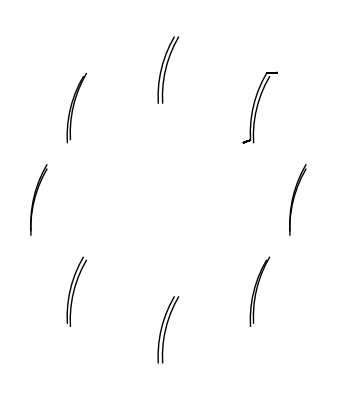

```mathematica
halfTooth={
Circle[{0,0},r1,{π/2,π-ArcCos[6/r1]}],
Circle[{0,0},r2,{π-ArcCos[15/r2],(π/2+2 π/16)}],
Circle[p3,r3,{θ1,2π+θ2}]};
rft=ReflectionTransform[{1,0}];
tooth={halfTooth,GeometricTransformation[halfTooth,rft]};
rot=RotationTransform[2π/8];
gr2D=Graphics[NestList[GeometricTransformation[#,rot]&,tooth,7]]
```

Next, we proceed to put the above insight into 3D. Since the Wolfram language does not have a Circle primitive that can be used in 3D OpenCascadeLink provides one. The primitive allows one to specify coordinates through which the circle should pass.

Compute the end point of the third arc.

```mathematica
N[p4=r2{Cos[θ],Sin[θ]}/.θ->(π/2+2 π/16)]
```

{-19.1342,46.194}

Setup the OpenCascade 3D Circle primitives:

```mathematica
c1=OpenCascadeCircle[{{0,0,0},{1,0,0}},r1,{{0,0,r1},Join[{0},p1]}];
c2=OpenCascadeCircle[{Join[{0},p3],{1,0,0}},r3,{Join[{0},p1],Join[{0},p2]}];
c3=OpenCascadeCircle[{{0,0,0},{1,0,0}},r2,{Join[{0},p2],Join[{0},p4]}];
```

Create OpenCascade shape objects:

```mathematica
shapes=OpenCascadeShape/@{c1,c2,c3};
```

Make a single wire from the arc segments:

```mathematica
ocHalfTooth=OpenCascadeShapeWire[shapes]
```

OpenCascadeShapeExpression[10]

Inspect the resulting type:

```mathematica
OpenCascadeShapeType[ocHalfTooth]
```

Wire

Next, the half tooth is mirrored along the Z-axis.

Set up a rotation transform in the Z-axis direction:

```mathematica
rot1=RotationTransform[Pi,{0,0,1}]
```

TransformationFunction[(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]

Create the full gear tooth by combining the half tooth and the mirrored half tooth:

```mathematica
ocTooth=OpenCascadeShapeWire[{ocHalfTooth,OpenCascadeShape[ocHalfTooth,rot1]}]
```

OpenCascadeShapeExpression[12]

Set up a rotation transforms in steps of of 2π/8 in the X-axis direction

```mathematica
rott=Table[RotationTransform[k*2π/8,{1,0,0}],{k,0,7}];
```

Create the gear profile wire in the YZ-axis by multiple rotations of the single tooth around the X-axis:

```mathematica
ocGearProfile1=OpenCascadeShapeWire[OpenCascadeShapeTransformation[ocTooth,#]&/@rott]
```

OpenCascadeShapeExpression[21]

To visualize the created gear profile in 3D we use a trick to give the flat profile an extension in the X-direction. This is purely for visualization and is not needed for the gear constriction.

Visualize the gear profile in 3D together with the shaft:

```mathematica
temp=OpenCascadeShapeLinearSweep[ocGearProfile1,{{0,0,0},{1,0,0}}];
Show[OpenCascadeShapeSurfaceMeshToBoundaryMesh[temp]["Wireframe"],shaftGR,OpenCascadeAxis3D[{-10,0,0},{200,75,75}]]
```

-Graphics3D-

#### Make planes

Now, the the gear profile is created that profile can be scaled, rotated and translated to create the gear profiles parallel to each other in the YZ-plane.

Create the second gear profile:

```mathematica
ocGearProfile2=OpenCascadeShapeTransformation[ocGearProfile1,ScalingTransform[0.75*{1,1,1},{0,0,0}]];
ocGearProfile2=OpenCascadeShapeTransformation[ocGearProfile2,RotationTransform[-15 Degree,{1,0,0}]];
ocGearProfile2=OpenCascadeShapeTransformation[ocGearProfile2,TranslationTransform[{-45,0,0}]];
```

Create the third gear profile:

```mathematica
ocGearProfile3=OpenCascadeShapeTransformation[ocGearProfile1,ScalingTransform[0.5*{1,1,1},{0,0,0}]];
ocGearProfile3=OpenCascadeShapeTransformation[ocGearProfile3,RotationTransform[-30 Degree,{1,0,0}]];
ocGearProfile3=OpenCascadeShapeTransformation[ocGearProfile3,TranslationTransform[{-95,0,0}]];
```

Visualize the gear profiles:

```mathematica
temp=OpenCascadeShapeLinearSweep[#,{{0,0,0},{2,0,0}}]&/@{ocGearProfile1,ocGearProfile2,ocGearProfile3};
Show[OpenCascadeShapeSurfaceMeshToBoundaryMesh[#]["Wireframe"["MeshElementStyle"->FaceForm[Red]]]&/@temp]
```

-Graphics3D-

Construct the full 3D gear by creating surfaces through the gear profiles in the YZ-panes:

```mathematica
gear=OpenCascadeShapeLoft[{ocGearProfile1,ocGearProfile2,ocGearProfile3},"BuildSolid"->True]
```

OpenCascadeShapeExpression[32]

Extract a boundary element mesh:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[gear];
```

Visualize the boundary element mesh of the gear:

```mathematica
Show[
gearGR=bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightGray]]]],
OpenCascadeAxis3D[{-100,0,0},{120,75,75}]]
```

-Graphics3D-

To verify that the boundary mesh construction worked as intended, a full element mesh is generated.

Create a full element mesh:

```mathematica
ToElementMesh[bmesh,"MeshOrder"->1]
```

ElementMesh[{{-95.,0.},{-85.,85.},{-85.,85.}},{TetrahedronElement[<24037>]}]

### Combine

The shaft and the gear are now combined.

Create the union of the shaft and the gear.

```mathematica
bevelGear=OpenCascadeShapeUnion[shaft,gear]
```

OpenCascadeShapeExpression[33]

Extract a boundary element mesh:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[bevelGear];
```

Visualize the boundary element mesh of the union of the shaft and the gear:

```mathematica
Show[
bevelGearGR=bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightGray]]]],
OpenCascadeAxis3D[{-100,0,0},{300,75,75}]]
```

-Graphics3D-

To verify that the boundary mesh construction worked as intended, a full element mesh is generated.

Create a full element mesh:

```mathematica
ToElementMesh[bmesh,"MeshOrder"->1]
```

ElementMesh[{{-95.,163.},{-85.,85.},{-85.,85.}},{TetrahedronElement[<24220>]}]

#### Boss

Create a Cuboid that will be used to make the bosses:

```mathematica
boss=Cuboid[{length-80,-5,36-2},{length-32,5,36+5}]
```

Cuboid[{83,-5,34},{131,5,41}]

Visualize the beveled gear and a single boss:

```mathematica
Show[bevelGearGR,Graphics3D[boss]]
```

-Graphics3D-

Verify the the boss does indeed intersect the surface of the shaft properly:

```mathematica
Show[bevelGearGR,Graphics3D[boss],PlotRange->((#+{-10,10})&/@Transpose[List@@boss])]
```

-Graphics3D-

Create 13 bosses:

```mathematica
s=OpenCascadeShape[boss];
num=13;
s=OpenCascadeShapeTransformation[s,#]&/@Table[RotationTransform[k*2π/num,{1,0,0}],{k,1,num}];
```

Form the union of the bosses with the beveled gear:

```mathematica
bevelGearBoss=OpenCascadeShapeUnion[Flatten[{bevelGear,s}]]
```

OpenCascadeShapeExpression[60]

Extract a boundary element mesh:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[bevelGearBoss];
```

Visualize the boundary element mesh of the union of the shaft and the gear:

```mathematica
Show[
bevelGearGR=bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightGray]]]],
OpenCascadeAxis3D[{-100,0,0},{300,75,75}]]
```

-Graphics3D-

To verify that the boundary mesh construction worked as intended, a full element mesh is generated.

Create a full element mesh:

```mathematica
ToElementMesh[bmesh,"MeshOrder"->1]
```

ElementMesh[{{-95.,163.},{-85.,85.},{-85.,85.}},{TetrahedronElement[<30773>]}]

#### Hollow shaft

Create a Cylinder to use to perforate the object:

```mathematica
cyl=Cylinder[{{-120,0,0},{200,0,0}},35/2]
```

Cylinder[{{-120,0,0},{200,0,0}},35/2]

Visualize the beveled gear and the cylinder that is to create the perforation:

```mathematica
Show[bevelGearGR,Graphics3D[cyl]]
```

-Graphics3D-

Create the difference of the beveled gear and the cylinder:

```mathematica
bevelGearBoss=OpenCascadeShapeDifference[bevelGearBoss,OpenCascadeShape[cyl]]
```

OpenCascadeShapeExpression[62]

Extract a boundary element mesh:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[bevelGearBoss];
```

Visualize the boundary element mesh of the union of the shaft and the gear:

```mathematica
Show[
bevelGearGR=bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightGray]]]],
OpenCascadeAxis3D[{-100,0,0},{300,75,75}]]
```

-Graphics3D-

To verify that the boundary mesh construction worked as intended, a full element mesh is generated.

Create a full element mesh:

```mathematica
ToElementMesh[bmesh,"MeshOrder"->1]
```

ElementMesh[{{-95.,163.},{-85.,85.},{-85.,85.}},{TetrahedronElement[<34843>]}]

Extract a boundary element mesh with a refined surface approximation:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[bevelGearBoss,"ShapeSurfaceMeshOptions"->{"LinearDeflection"->0.001}];
```

```mathematica
Show[
bevelGearGR=bmesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightGray]]]],
OpenCascadeAxis3D[{-100,0,0},{300,75,75}]]
```

-Graphics3D-

Create a full mesh and visualize the beveled gear:

```mathematica
mesh=ToElementMesh[bmesh,"MeshOrder"->1,"MaxCellMeasure"->Infinity];
Show[mesh["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightGray],EdgeForm[]]]],
mesh["Edgeframe"]]
```

-Graphics3D-

#### Initialization

The following helper function is to visualize circles in 3D space.

```mathematica
Circle3D[{centre_,normal_},radius_:1,angle_:{0,2 Pi}]:=
Module[{r,mp,mp3D},
r=DiscretizeGraphics[Circle[centre[[{1,2}]],radius,angle]];
mp=MeshPrimitives[r,1,Multicells->True];
mp3D=mp/.{x_Real,y_Real}:>{x,y,centre[[3]]};
RotationTransform[{{0,0,1},normal},centre]/@mp3D
]
```

#### References

[1] https://www.youtube.com/watch?v=VihInzgm0QA

More About

Related Tutorials

Using OpenCascde Link

Related Wolfram Training Courses